```mathematica
"192.168.1.1/0/dev1"
```

```mathematica
id1="addr1/0/dev1";
id2="addr2/0/dev2";
id3="addr2/0/dev3";
id4="addr3/0/dev4";
```

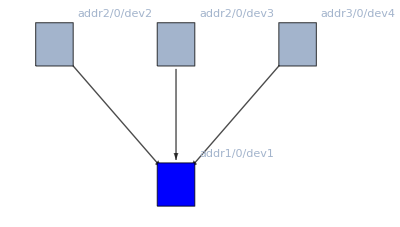

```mathematica
GraphPlot[Graph[{id2->id1,id3->id1,id4->id1}],VertexSize->0.35,VertexShapeFunction->"Square",VertexLabels->"Name",VertexStyle->{id1->Blue},EdgeStyle->Directive[Thick,Black]]
```

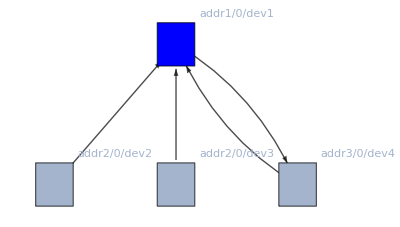

```mathematica
Graph[{id2->id1,id3->id1,id4->id1,id1->id4},VertexSize->0.35,VertexShapeFunction->"Square",VertexLabels->"Name",VertexStyle->{id1->Blue},EdgeStyle->Directive[Thick,Black],GraphLayout->"LayeredEmbedding"]
```

```mathematica
VertexLabels->Table[i->Placed["■",p],{i,3}]
```

VertexLabels→{1→Placed[■,p],2→Placed[■,p],3→Placed[■,p]}

## STI network graphs figures

```mathematica
id1="addr1/0/dev1";
id2="addr2/0/dev2";
id3="addr2/0/dev3";
id4="addr3/0/dev4";
```

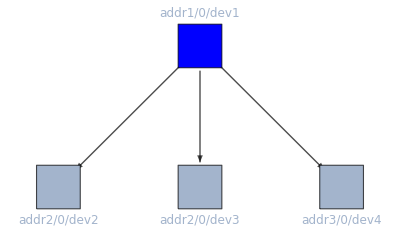

```mathematica
net1={id1->id2,id1->id3,id1->id4};
g1=Graph[net1,VertexSize->0.35,VertexShapeFunction->"Square",VertexStyle->{id1->Blue},EdgeStyle->Directive[Thick,Black],GraphLayout->"LayeredEmbedding",VertexLabels->(((#->Placed[Style[#,FontSize->12],Below])&/@{id2,id3,id4})~Join~{id1->Placed[Style[id1,FontSize->12],Above]})]
```

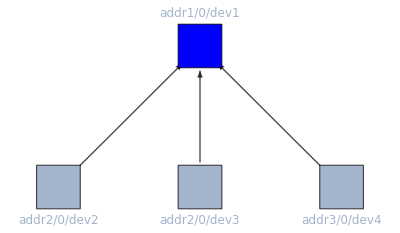

```mathematica
g1=Graph[{id2->id1,id3->id1,id4->id1},VertexSize->0.35,VertexShapeFunction->"Square",VertexStyle->{id1->Blue},EdgeStyle->Directive[Thick,Black],GraphLayout->"LayeredEmbedding",VertexLabels->(((#->Placed[Style[#,FontSize->12],Below])&/@{id2,id3,id4})~Join~{id1->Placed[Style[id1,FontSize->12],Above]})]
```

```mathematica
Export[NotebookDirectory[]<>"stinet1.png",g1]
```

/home/hogan/code/dev/sti3/docs/figs/stinet1.png

```mathematica
id1="addr1/0/dev1";
id2="addr2/0/dev2";
id3="addr2/0/dev3";
id4="addr3/0/dev4";
id5="addr4/0/dev5";
id6="addr4/0/dev6";
```

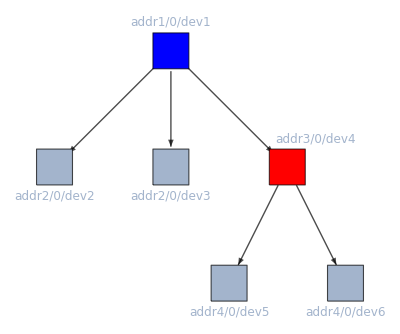

```mathematica
net2={id1->id2,id1->id3,id1->id4,id4->id5,id4->id6};
g2=Graph[net2,VertexSize->0.35,VertexShapeFunction->"Square",VertexStyle->{id1->Blue,id4->Red},EdgeStyle->Directive[Thick,Black],GraphLayout->"LayeredEmbedding",VertexLabels->(((#->Placed[Style[#,FontSize->12],Below])&/@{id2,id3,id5,id6})~Join~{id1->Placed[Style[id1,FontSize->12],Above],id4->Placed[Style[id4,FontSize->12],{1.2,1.2}]})]
```

```mathematica
Export[NotebookDirectory[]<>"stinet2.png",g2]
```

/home/hogan/code/dev/sti3/docs/figs/stinet2.png

```mathematica
id1="addr1/0/dev1";
id2="addr2/0/dev2";
id3="addr2/0/dev3";
id4="addr3/0/dev4";
id5="addr4/0/dev5";
id6="addr4/0/dev6";
id7="addr1/0/dev7";
id8="addr5/0/dev8";
```

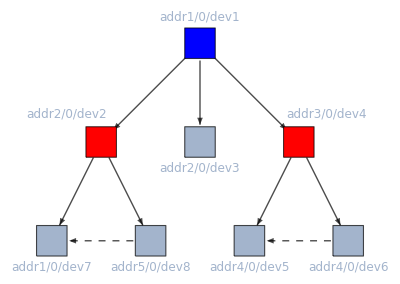

```mathematica
serverEdges={id1->id2,id1->id3,id1->id4,id4->id5,id4->id6,id2->id7,id2->id8};
deviceEdges={id8->id7,id6->id5};
g3=Graph[serverEdges~Join~deviceEdges,VertexSize->0.35,VertexShapeFunction->"Square",VertexStyle->{id1->Blue,id4->Red,id2->Red},GraphLayout->"LayeredEmbedding",VertexLabels->(((#->Placed[Style[#,FontSize->12],Below])&/@{id2,id3,id5,id6,id7,id8})~Join~{id1->Placed[Style[id1,FontSize->12],Above],id4->Placed[Style[id4,FontSize->12],{1.3,1.3}],id2->Placed[Style[id2,FontSize->12],{-0.5,1.3}]}),
EdgeStyle->(
((#->Directive[Thick,Black])&/@serverEdges)~Join~((#->Directive[Thick,Black,Dashed])&/@deviceEdges)
)]
```

```mathematica
Export[NotebookDirectory[]<>"stinet3.png",g3]
```

/home/hogan/code/dev/sti3/docs/figs/stinet3.png

```mathematica
AbsoluteOptions[g3,VertexCoordinates]
```

{VertexCoordinates→{{0.438529,0.877058},{1.31559,1.75412},{1.31559,0.877058},{2.19265,0.877058},{1.75412,0.},{2.63117,0.},{0.,0.},{0.877058,0.}}}

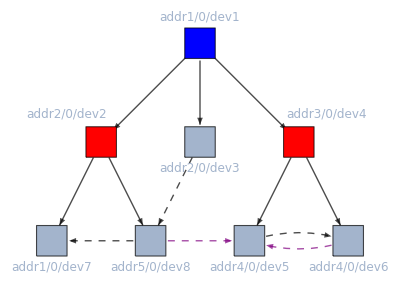

```mathematica
serverEdges={id1->id2,id1->id3,id1->id4,id4->id5,id4->id6,id2->id7,id2->id8};
deviceEdges={id8->id7,id5->id6,id3->id8};
eventTargetEdges={id6->id5,id8->id5};
g3b=Graph[serverEdges~Join~deviceEdges~Join~eventTargetEdges,VertexSize->0.35,VertexShapeFunction->"Square",VertexStyle->{id1->Blue,id4->Red,id2->Red},GraphLayout->"LayeredEmbedding",VertexLabels->(((#->Placed[Style[#,FontSize->12],Below])&/@{id2,id3,id5,id6,id7,id8})~Join~{id1->Placed[Style[id1,FontSize->12],Above],id4->Placed[Style[id4,FontSize->12],{1.3,1.3}],id2->Placed[Style[id2,FontSize->12],{-0.5,1.3}]}),
EdgeStyle->(
((#->Directive[Thick,Black])&/@serverEdges)~Join~((#->Directive[Thick,Black,Dashed])&/@deviceEdges)~Join~((#->Directive[Thick,Purple,Dashed])&/@eventTargetEdges)
),AbsoluteOptions[g3,VertexCoordinates]]
```

```mathematica
Export[NotebookDirectory[]<>"stinet4.png",g3b]
```

/home/hogan/code/dev/sti3/docs/figs/stinet4.png

## Hub figures

```mathematica
id1="addr1/0/dev1";
id2="addr2/0/dev2";
id3="addr2/0/dev3";
id4="addr3/0/dev4";
id5="addr4/0/dev5";
id6="addr4/0/dev6";
id7="addr1/0/dev7";
id8="addr5/0/dev8";
```

```mathematica
hid1="addr1/0/hub1";
hid2="addr2/0/hub2";
hid3="addr3/0/hub3";
hid4="addr4/0/hub4";
```

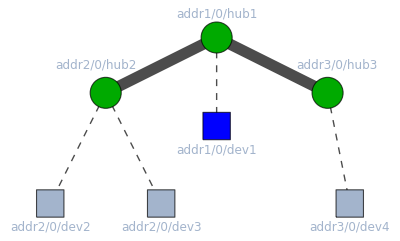

```mathematica
hubs={hid1<->hid2,hid1<->hid3};
devs={hid1<->id1,hid2<->id2,hid2<->id3,hid3<->id4};
h1=Graph[hubs~Join~devs,VertexSize->0.35,VertexShapeFunction->((#->"Circle"&/@{hid1,hid2,hid3})~Join~(#->"Square"&/@{id1,id2,id3,id4})),
VertexStyle->({id1->Blue}~Join~(#->Darker[Green]&/@{hid1,hid2,hid3})),
DirectedEdges->False,
GraphLayout->"LayeredEmbedding",
(*GraphLayout->{"LayeredEmbedding", "Orientation"->Top,LayerSizeFunction->(6&),"LeafDistance"->5},*)
(*GraphLayout->{"StarEmbedding", "Offset"->127 Degree},*)
VertexLabels->({
(#->Placed[Style[#,FontSize->12],Above])&[hid1],
(#->Placed[Style[#,FontSize->12],{0.2,1.4}])&[hid2],
(#->Placed[Style[#,FontSize->12],{0.8,1.4}])&[hid3]}~Join~((#->Placed[Style[#,FontSize->12],Below])&/@{id1,id2,id3,id4})),
EdgeStyle->(
((#->Directive[Thickness[0.02],Black])&/@hubs)~Join~((#->Directive[Thick,Black,Dashed])&/@devs)
),
VertexCoordinates->{{0,0.5},{-1,0.0},{1,0},
{0,-0.3},{-1.5,-1},{-0.5,-1},{1.2,-1}}
]
```

```mathematica
Export[NotebookDirectory[]<>"stihubnet1.png",h1]
```

/home/hogan/code/dev/sti3/docs/figs/stihubnet1.png

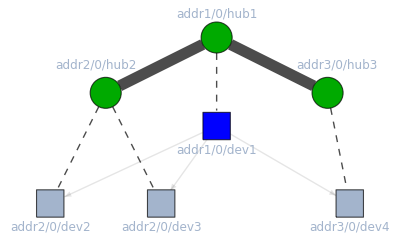

```mathematica
hubs={hid1<->hid2,hid1<->hid3};
devs={hid1<->id1,hid2<->id2,hid2<->id3,hid3<->id4};
h1b=Graph[hubs~Join~devs~Join~net1,VertexSize->0.35,VertexShapeFunction->((#->"Circle"&/@{hid1,hid2,hid3})~Join~(#->"Square"&/@{id1,id2,id3,id4})),
VertexStyle->({id1->Blue}~Join~(#->Darker[Green]&/@{hid1,hid2,hid3})),
DirectedEdges->False,
GraphLayout->"LayeredEmbedding",
(*GraphLayout->{"LayeredEmbedding", "Orientation"->Top,LayerSizeFunction->(6&),"LeafDistance"->5},*)
(*GraphLayout->{"StarEmbedding", "Offset"->127 Degree},*)
VertexLabels->({
(#->Placed[Style[#,FontSize->12],Above])&[hid1],
(#->Placed[Style[#,FontSize->12],{0.2,1.4}])&[hid2],
(#->Placed[Style[#,FontSize->12],{0.8,1.4}])&[hid3]}~Join~((#->Placed[Style[#,FontSize->12],Below])&/@{id1,id2,id3,id4})),
EdgeStyle->(
((#->Directive[Thickness[0.02],Black])&/@hubs)~Join~((#->Directive[Thick,Black,Dashed])&/@devs)~Join~((#->Directive[Thick,Black,Opacity[0.1]])&/@net1)
),
VertexCoordinates->{{0,0.5},{-1,0.0},{1,0},
{0,-0.3},{-1.5,-1},{-0.5,-1},{1.2,-1}}
]
```

```mathematica
Export[NotebookDirectory[]<>"stihubnet1.png",h1b]
```

/home/hogan/code/dev/sti3/docs/figs/stihubnet1.png

```mathematica
AbsoluteOptions[h1,VertexCoordinates]
```

{VertexCoordinates→{{0.,0.},{0.999848,0.0174524},{0.292372,0.956305},{-0.819152,0.573576},{-0.798636,-0.601815},{0.325568,-0.945519}}}

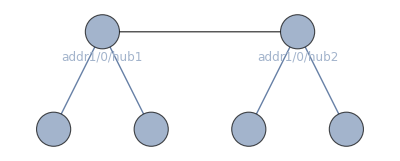

```mathematica
Graph[hubs~Join~devs,VertexSize->0.35,VertexShapeFunction->"Circle",DirectedEdges->False,
(*GraphLayout->{"LayeredEmbedding", "Orientation"->Top,LayerSizeFunction->(6&),"LeafDistance"->5},*)
GraphLayout->{"StarEmbedding", "Offset"->127 Degree},
VertexLabels->(((#->Placed[Style[#,FontSize->12],Below])&/@{hid1,hid2})~Join~{}),
EdgeStyle->(
((#->Directive[Thick,Black])&/@hubs)~Join~((#->Directive[Thick,Black,Dashed])&/@{})
),VertexCoordinates->{{0,0},{2,0},{0.5,-1},{-0.5,-1},{1.5,-1},{2.5,-1}}]
```

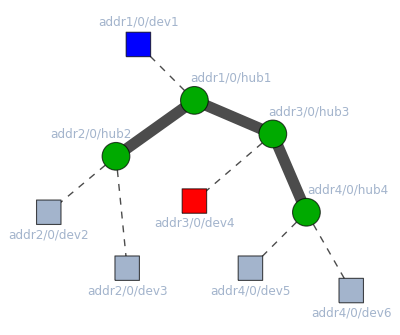

```mathematica
hubs={hid1->hid2,hid1->hid3,hid3->hid4};
devs={hid1->id1,hid2->id2,hid2->id3,hid3->id4,hid4->id5,hid4->id6};
h2=Graph[hubs~Join~devs,VertexSize->0.35,VertexShapeFunction->((#->"Circle"&/@{hid1,hid2,hid3,hid4})~Join~(#->"Square"&/@{id1,id2,id3,id4,id5,id6})),
VertexStyle->({id1->Blue,id4->Red}~Join~(#->Darker[Green]&/@{hid1,hid2,hid3,hid4})),
DirectedEdges->False,
(*GraphLayout->"LayeredEmbedding",*)
GraphLayout->{"LayeredEmbedding", "Orientation"->Top},
(*GraphLayout->{"StarEmbedding", "Offset"->127 Degree},*)
VertexLabels->(((#->Placed[Style[#,FontSize->12],Above])&/@{})~Join~((#->Placed[Style[#,FontSize->12],Below])&/@{id2,id3,id4,id5,id6})~Join~{(#->Placed[Style[#,FontSize->12],Above])&[id1],
(#->Placed[Style[#,FontSize->12],{1.8,1.3}])&[hid1],
(#->Placed[Style[#,FontSize->12],{-0.4,1.3}])&[hid2],
(#->Placed[Style[#,FontSize->12],{1.8,1.3}])&[hid3],
(#->Placed[Style[#,FontSize->12],{2,1.3}])&[hid4]}),
EdgeStyle->(
((#->Directive[Thickness[0.02],Black])&/@hubs)~Join~((#->Directive[Thick,Black,Dashed])&/@devs)
),
VertexCoordinates->{
{1.5,2.6},(*hub1*)
{0.8,2.1},(*hub2*)
{2.2,2.3},(*hub3*)
{2.5,1.6},(*hub4*)
{1.0,3.1},(*dev1*)
{0.2,1.6},(*dev2*)
{0.9,1.1},(*dev3*)
{1.5,1.7},(*dev4*)
{2.0,1.1},(*dev5*)
{2.9,0.9} (*dev6*)
}
]
```

```mathematica
Export[NotebookDirectory[]<>"stihubnet2.png",h2]
```

```mathematica
VertexCoordinates->{
{1.5,2.6},(*hub1*)
{0.7,1.8},(*hub2*)
{2.3,2.2},(*hub3*)
{3,1.5},(*hub4*)
{1.5,1.5},(*dev1*)
{-0.2,0.8},(*dev2*)
{0.8,0.8},(*dev3*)
{2.3,0.8},(*dev4*)
{3,0.5},(*dev5*)
{3.7,0.9} (*dev6*)
}
```

```mathematica
AbsoluteOptions[h2,VertexCoordinates]
```

{VertexCoordinates→{{1.53644,2.30466},{0.384111,1.53644},{1.92055,1.53644},{1.53644,0.768221},{2.68877,1.53644},{0.,0.768221},{0.768221,0.768221},{2.30466,0.768221},{1.15233,0.},{1.92055,0.}}}

```mathematica
net2
```

{addr1/0/dev1->addr2/0/dev2,addr1/0/dev1->addr2/0/dev3,addr1/0/dev1->addr3/0/dev4,addr3/0/dev4→addr4/0/dev5,addr3/0/dev4→addr4/0/dev6}

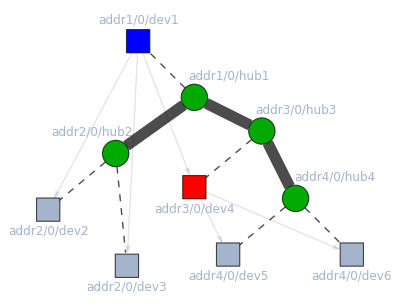

```mathematica
hubs={hid1<->hid2,hid1<->hid3,hid3<->hid4};
devs={hid1<->id1,hid2<->id2,hid2<->id3,hid3<->id4,hid4<->id5,hid4<->id6};
h3=Graph[hubs~Join~devs~Join~net2,VertexSize->0.35,VertexShapeFunction->((#->"Circle"&/@{hid1,hid2,hid3,hid4})~Join~(#->"Square"&/@{id1,id2,id3,id4,id5,id6})),
VertexStyle->({id1->Blue,id4->Red}~Join~(#->Darker[Green]&/@{hid1,hid2,hid3,hid4})),
DirectedEdges->True,
(*GraphLayout->"LayeredEmbedding",*)
GraphLayout->{"LayeredEmbedding", "Orientation"->Top},
(*GraphLayout->{"StarEmbedding", "Offset"->127 Degree},*)
VertexLabels->(((#->Placed[Style[#,FontSize->12],Above])&/@{})~Join~((#->Placed[Style[#,FontSize->12],Below])&/@{id2,id3,id4,id5,id6})~Join~{(#->Placed[Style[#,FontSize->12],Above])&[id1],
(#->Placed[Style[#,FontSize->12],{1.8,1.3}])&[hid1],
(#->Placed[Style[#,FontSize->12],{-0.4,1.3}])&[hid2],
(#->Placed[Style[#,FontSize->12],{1.8,1.3}])&[hid3],
(#->Placed[Style[#,FontSize->12],{2,1.3}])&[hid4]}),
EdgeStyle->(
((#->Directive[Thickness[0.02],Black])&/@hubs)~Join~((#->Directive[Thick,Black,Dashed])&/@devs)~Join~((#->Directive[Thick,Black,Opacity[0.1]])&/@net2)
),
VertexCoordinates->{
{1.5,2.6},(*hub1*)
{0.8,2.1},(*hub2*)
{2.1,2.3},(*hub3*)
{2.4,1.7},(*hub4*)
{1.0,3.1},(*dev1*)
{0.2,1.6},(*dev2*)
{0.9,1.1},(*dev3*)
{1.5,1.8},(*dev4*)
{1.8,1.2},(*dev5*)
{2.9,1.2} (*dev6*)
}
]
```

```mathematica
Export[NotebookDirectory[]<>"stihubnet2.png",h3]
```

/home/hogan/code/dev/sti3/docs/figs/stihubnet2.png